## Matrices

```mathematica
σx=({{0, 1}, {1, 0}});
σy=({{0, -I}, {I, 0}});
σz=({{1, 0}, {0, -1}});
matrices={σx,σy,σz};
coefs={λx,λy,λz};
Operator=λx*σx+λy*σy+λz*σz;
```

## Commutators

```mathematica
σxCommutator=σx.Operator-Operator.σx;
σyCommutator=σy.Operator-Operator.σy;
σzCommutator=σz.Operator-Operator.σz;
```

## Thermodynamics Functions

```mathematica
MeanFieldHamiltonian[q_,J_,B_,Oz_]:=B*σx-J/2 Oz*σz+J/4 Oz^2*IdentityMatrix[2];
Z[β_,q_,J_,B_,Oz_]:=Tr[MatrixExp[-β*MeanFieldHamiltonian[q,J,B,Oz]]];
F[β_,q_,J_,B_,Oz_]:=-1/β Log[Z[β,q,J,B,Oz]]
```

## Dynamics Equation

```mathematica
DynamicsEquation[Q_,J_, B_,Oz_,OzComm_]:=B*σxCommutator-J/4(Q*OzComm*σz+Oz*σzCommutator);
```

(-1.01 (0.+OzComm Q)+(0.+0.402 ⅈ) λy | 3.04832×10^-6 (2 λx-2 ⅈ λy)-0.402 λz
3.04832×10^-6 (-2 λx-2 ⅈ λy)+0.402 λz | -1.01 (0.-OzComm Q)-(0.+0.402 ⅈ) λy)

## Dynamics Solver

```mathematica
ClearAll[T0,q0,θ,Q0,J,B0,freqArr,OzArr,ExpσxArr,ExpσyArr,ExpσzArr,probs,Bmin,Bmax,dB]
```

```mathematica
T0=.01;
q0=1;
θ=0;
Q0=2*Cos[θ];
J0=0.1;
freqArr={};
OzArr={};
ExpσxArr={};
ExpσyArr={};
ExpσzArr={};
energies = {};
coefArr={};
waveFuncArr={};
probs={};
(*Loop over magnetic field*)
Bmin=0;Bmax=.2;dB=.001;
Monitor[For[B=Bmin, B<=Bmax,B+=dB,
	(*Minimize Free Energy w.r.t. Order parameters*)
	Oz=O/.FindMinimum[{F[1/T0,q0,J0,B,O],O<=5},{O,1}][[2]];
	AppendTo[OzArr,{B,Oz}];
	(*Solve MFT Hamiltonian*)
	{{E1,E2},{ψ1,ψ2}}=Eigensystem[MeanFieldHamiltonian[q0,J0,B,Oz]];
	AppendTo[energies,{B,E1,E2}];
	(*Calculate Probabilities*)
	z=Exp[-E1/T0]+Exp[-E2/T0];
	p1=Exp[-E1/T0]/z;
	p2=Exp[-E2/T0]/z;
	AppendTo[probs,{B,p1,p2}];
	(*Evaluate Expectation Values*)
	Expσx=p1*ConjugateTranspose[ψ1].σx.ψ1+p2*ConjugateTranspose[ψ2].σx.ψ2;
	Expσy=p1*ConjugateTranspose[ψ1].σy.ψ1+p2*ConjugateTranspose[ψ2].σy.ψ2;
	Expσz=p1*ConjugateTranspose[ψ1].σz.ψ1+p2*ConjugateTranspose[ψ2].σz.ψ2;
	ExpσzComm=p1*ConjugateTranspose[ψ1].σzCommutator.ψ1+p2*ConjugateTranspose[ψ2].σzCommutator.ψ2;
	AppendTo[ExpσxArr,{B,Expσx}];
	AppendTo[ExpσyArr,{B,Expσy}];
	AppendTo[ExpσzArr,{B,Expσz}];
	(*Calculate Equation Coefficients *)
	EquationCoefs=ConstantArray[0,{3,3}];
	For[i=1,i<=3,i++,
	For[j=1,j<=3,j++,
	EquationCoefs[[i,j]]=.5(Tr[DynamicsEquation[Q0,J0,B,Expσz,ExpσzComm].matrices[[i]]]/.{Table[If[k!=j,coefs[[k]]->0,coefs[[k]]->1],{k,1,3}]})[[1]];
	];	
	];
	freqs=Sort[Eigenvalues[EquationCoefs]];
	coefVecs=Eigenvectors[EquationCoefs];
	For[l=1,l<=Length[coefVecs],l++,
		AppendTo[coefArr,Join[{B},coefVecs[[l]]]]
	];
	AppendTo[freqArr,Join[{B},freqs]];
];,{B,Dimensions[coefVecs]}]
```

```mathematica
MatrixForm[EquationCoefs]
```

(0. | 0.-1.50907×10^-7 ⅈ | 0.
0.+1.50907×10^-7 ⅈ | 0.+0. ⅈ | 0.-0.4 ⅈ
0.+0. ⅈ | 0.+1.14075×10^-13 ⅈ | 0.+0. ⅈ)

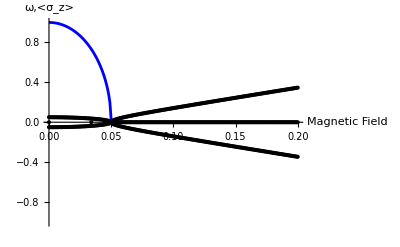

```mathematica
p1=ListLinePlot[OzArr,PlotStyle->Blue];
p2=ListPlot[{energies[[;;,{1,2}]],energies[[;;,{1,3}]]}];
p3=ListLinePlot[{ExpσxArr,ExpσyArr,ExpσzArr},PlotLegends->{"<σx>","<σy>","<σz>"}];
p4=ListPlot[Table[freqArr[[;;,{1,i}]],{i,2,4}],PlotStyle->Black];
p5=Plot[{√(4 h^2-Q0*h*J0),-√(4 h^2-Q0*h*J0)},{h,Bmin,Bmax},PlotStyle->Black];
p6=ListPlot[Table[Table[Join[{coefArr[[i,1]]},Table[Re[coefArr[[i,j]]],{j,2,4}]],{i,1,Length[coefArr]}][[;;,{1,k}]],{k,2,4}],PlotLegends->{"Re[λ_x]", "Re[λ_y]", "Re[λ_z]"}, AxesLabel->{"Magnetic Field Strength"},PlotMarkers->{Red,Blue,Green}];
p7=ListPlot[Table[Table[Join[{coefArr[[i,1]]},Table[Im[coefArr[[i,j]]],{j,2,4}]],{i,1,Length[coefArr]}][[;;,{1,k}]],{k,2,4}],PlotLegends->{"Im[λ_x]", "Im[λ_y]", "Im[λ_z]"}, AxesLabel->{"Magnetic Field Strength"},PlotMarkers->{Purple,Orange,Yellow}];
p8=ListPlot[Table[Table[Join[{coefArr[[i,1]]},Table[Abs[coefArr[[i,j]]],{j,2,4}]],{i,1,Length[coefArr]}][[;;,{1,k}]],{k,2,4}],PlotLegends->{"Abs[λ_x]", "Abs[λ_y]", "Abs[λ_z]"}, AxesLabel->{"Magnetic Field Strength"},PlotMarkers->{{Red,4},{Green,4},{Blue,4}}];
p9=ListPlot[Table[probs[[;;,{1,i}]],{i,2,3}]];
Show[{p1,p4},PlotRange->{-10^0,10^-0},AxesLabel->{"Magnetic Field", "ω,<σ_z>"}]
```

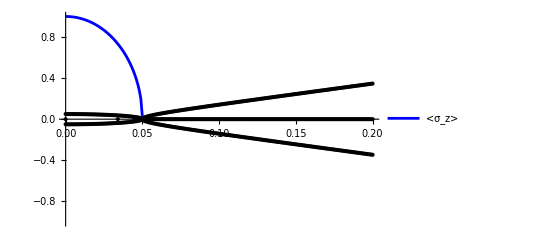

```mathematica
ClearAll[Q0,J0,B,Expσz,ExpσzComm]
EquationCoefs=ConstantArray[0,{3,3}];
	For[i=1,i<=3,i++,
	For[j=1,j<=3,j++,
	EquationCoefs[[i,j]]=.5(Tr[DynamicsEquation[Q0,J0,B,Expσz,ExpσzComm].matrices[[i]]]/.{Table[If[k!=j,coefs[[k]]->0,coefs[[k]]->1],{k,1,3}]})[[1]];
	];	
	];
```

```mathematica
MatrixForm[EquationCoefs]
```

(0. | (0.+2. ⅈ) Expσz J0 | 0.
(0.-2. ⅈ) Expσz J0 | 0. | (0.-2. ⅈ) B
-1. ExpσzComm J0 Q0 | 0.5 (4 ⅈ B-2 ExpσzComm J0 Q0) | -1. ExpσzComm J0 Q0)

## Variable Interaction Dynamics Solver

```mathematica
ClearAll[T0,q0,θ,Q0,J,B0,freqArr,OzArr,ExpσxArr,ExpσyArr,ExpσzArr,probs,Bmin,Bmax,dB]
```

```mathematica
T0=.01;
q0=2;
θ=0;
Q0=2*Cos[θ];
B0=0.1;
freqArr={};
OzArr={};
ExpσxArr={};
ExpσyArr={};
ExpσzArr={};
energies = {};
states={};
probs={};
coefArr={};
(*Loop over magnetic field*)
Jmin=.01;Jmax=1;dJ=.01;
Monitor[For[J=Jmin, J<=Jmax,J+=dJ,
	(*Minimize Free Energy w.r.t. Order parameters*)
	Oz=O/.FindMinimum[{F[1/T0,q0,J,B0,O],O<=5},{O,1}][[2]];
	AppendTo[OzArr,{J,Oz}];
	(*Solve MFT Hamiltonian*)
	{{E1,E2},{ψ1,ψ2}}=Eigensystem[MeanFieldHamiltonian[q0,J,B0,Oz]];
	AppendTo[energies,{J,E1,E2}];
	AppendTo[states,{J,ψ1,ψ2}];
	(*Calculate Probabilities*)
	z=Exp[-E1/T0]+Exp[-E2/T0];
	p1=Exp[-E1/T0]/z;
	p2=Exp[-E2/T0]/z;
	px=p1*Abs[ψ1[[1]]]^2+p2*Abs[ψ2[[1]]]^2;
	py=p1*Abs[ψ1[[2]]]^2+p2*Abs[ψ2[[2]]]^2;
	AppendTo[probs,{J,p1,p2,px,py}];
	(*Evaluate Expectation Values*)
	Expσx=p1*ConjugateTranspose[ψ1].σx.ψ1+p2*ConjugateTranspose[ψ2].σx.ψ2;
	Expσy=p1*ConjugateTranspose[ψ1].σy.ψ1+p2*ConjugateTranspose[ψ2].σy.ψ2;
	Expσz=p1*ConjugateTranspose[ψ1].σz.ψ1+p2*ConjugateTranspose[ψ2].σz.ψ2;
	ExpσzComm=p1*ConjugateTranspose[ψ1].σzCommutator.ψ1+p2*ConjugateTranspose[ψ2].σzCommutator.ψ2;
	AppendTo[ExpσxArr,{J,Expσx}];
	AppendTo[ExpσyArr,{J,Expσy}];
	AppendTo[ExpσzArr,{J,Expσz}];
	(*Calculate Equation Coefficients *)
	EquationCoefs=ConstantArray[0,{3,3}];
	For[i=1,i<=3,i++,
	For[j=1,j<=3,j++,
	EquationCoefs[[i,j]]=.5*(Tr[DynamicsEquation[Q0,J,B0,Expσz,ExpσzComm].matrices[[i]]]/.{Table[If[k!=j,coefs[[k]]->0,coefs[[k]]->1],{k,1,3}]})[[1]];
	];
	];
	freqs=Sort[Eigenvalues[EquationCoefs]];
	coefVecs=Eigenvectors[EquationCoefs];
	For[l=1,l<=Length[coefVecs],l++,
		AppendTo[coefArr,Join[{J},coefVecs[[l]]]]
	];
	AppendTo[freqArr,Join[{J},freqs]];
];,{J,Dimensions[coefVecs]}]
```

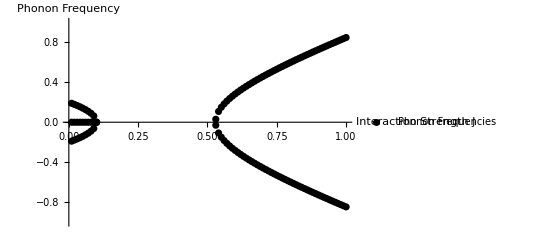

```mathematica
p1=ListPlot[OzArr];
p2=ListPlot[{energies[[;;,{1,2}]],energies[[;;,{1,3}]]}];
p3=ListLinePlot[{ExpσxArr,ExpσyArr,ExpσzArr},PlotLegends->{"<σx>","<σy>","<σz>"}];
p4=ListPlot[Table[freqArr[[;;,{1,i}]],{i,2,4}],PlotStyle->Black,PlotLegends->{"Phonon Frequencies"}];
p5=Plot[{√(4 B0^2-2*Q0*B0*j),-√(4 B0^2-2*Q0*B0*j)},{j,Jmin,Jmax},PlotStyle->Black,PlotLegends->{"+/-√(4 SuperscriptBox[B, 2] - 2 SubscriptBox[Q, 0] BJ)"}];
p6=ListPlot[{probs[[;;,{1,4}]],probs[[;;,{1,5}]]},PlotLegends->{"p_up","p_down"},PlotRange->{0,1}];
p7=ListPlot[Table[Abs[coefArr[[;;,{1,i}]]],{i,2,4}],PlotLegends->{"σ_x Coefficient", "σ_y Coefficient", "σ_z Coefficient"}, AxesLabel->{"Interaction Strength"},PlotMarkers->{{Automatic,3}}];
Show[{p4},PlotRange->{{0,Jmax},{-1,1}},AxesLabel->{"Interaction Strength J", "Phonon Frequency"}]
```

## Variable B and J Dynamics Solver

```mathematica
T0=.01;
q0=2;
θ=0;
Q0=2*Cos[θ];
freqArr={};
OzArr={};
ExpσxArr={};
ExpσyArr={};
ExpσzArr={};
energies = {};
coefArr={};
waveFuncArr={};
probs={};
(*Loop over magnetic field*)
Bmin=0;Bmax=.2;dB=.01;
Jmin=0;Jmax=1;dJ=.05;
Monitor[For[J=Jmin, J<=Jmax,J+=dJ,
For[B=Bmin, B<=Bmax,B+=dB,
	(*Minimize Free Energy w.r.t. Order parameters*)
	Oz=O/.FindMinimum[{F[1/T0,q0,J,B,O],O<=5},{O,1}][[2]];
	AppendTo[OzArr,{J,B,Oz}];
	(*Solve MFT Hamiltonian*)
	{{E1,E2},{ψ1,ψ2}}=Eigensystem[MeanFieldHamiltonian[q0,J,B,Oz]];
	AppendTo[energies,{J,B,E1,E2}];
	(*Calculate Probabilities*)
	z=Exp[-E1/T0]+Exp[-E2/T0];
	p1=Exp[-E1/T0]/z;
	p2=Exp[-E2/T0]/z;
	AppendTo[probs,{J,B,p1,p2}];
	(*Evaluate Expectation Values*)
	Expσx=p1*ConjugateTranspose[ψ1].σx.ψ1+p2*ConjugateTranspose[ψ2].σx.ψ2;
	Expσy=p1*ConjugateTranspose[ψ1].σy.ψ1+p2*ConjugateTranspose[ψ2].σy.ψ2;
	Expσz=p1*ConjugateTranspose[ψ1].σz.ψ1+p2*ConjugateTranspose[ψ2].σz.ψ2;
	ExpσzComm=p1*ConjugateTranspose[ψ1].σzCommutator.ψ1+p2*ConjugateTranspose[ψ2].σzCommutator.ψ2;
	AppendTo[ExpσxArr,{J,B,Expσx}];
	AppendTo[ExpσyArr,{J,B,Expσy}];
	AppendTo[ExpσzArr,{J,B,Expσz}];
	(*Calculate Equation Coefficients *)
	EquationCoefs=ConstantArray[0,{3,3}];
	For[i=1,i<=3,i++,
	For[j=1,j<=3,j++,
	EquationCoefs[[i,j]]=.5(Tr[DynamicsEquation[Q0,J,B,Expσz,ExpσzComm].matrices[[i]]]/.{Table[If[k!=j,coefs[[k]]->0,coefs[[k]]->1],{k,1,3}]})[[1]];
	];	
	];
	freqs=Sort[Eigenvalues[EquationCoefs]];
	coefVecs=Eigenvectors[EquationCoefs];
	For[l=1,l<=Length[coefVecs],l++,
		AppendTo[coefArr,Join[{J,B},coefVecs[[l]]]]
	];
	AppendTo[freqArr,{J,B,Max[Abs[freqs]]}];
];];
,{J,B,Dimensions[coefVecs]}]
```

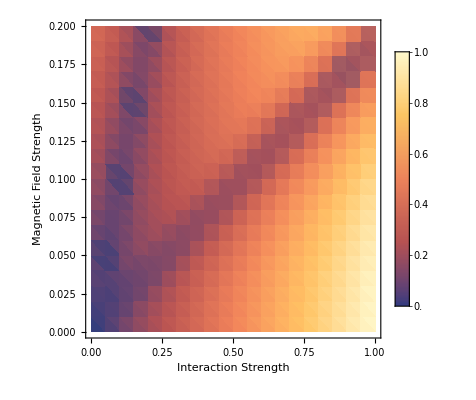

{}

```mathematica
ListDensityPlot[freqArr[[;;,{1,2,3}]],FrameLabel->{"Interaction Strength", "Magnetic Field Strength"},PlotLegends->Automatic]
```

## Analytic Calculations

```mathematica
MatrixForm[Simplify[ToRadicals[Eigenvalues[I*({{0, -J*sz, 0}, {J*sz, 0, 2*h}, {J*Q*sy, -2*h-1/2 J*Q*sx, 0}})]]/.{sx->-1,sy->0},Assumptions->{h>=0,J>=0,Q>=0,2h-J*Q>=0,sz>=0}]]
Manipulate[Plot[√(4 h^2-2 h J*.1+J^2 sz^2),{h,0,.25}],{sz,0,1},{J,0,1}]
```

(0
-√(4 h^2-h J Q+J^2 sz^2)
√(4 h^2-h J Q+J^2 sz^2))